# Vibration characteristics of a two story building

Julian Ly Davis

## Description:

## Often times buildings can be modeled as if the floors have independent mass supported by beams of measurable stiffness. Here we will use Mathematica to determine frequency response (transfer functions) of a two story house

Learning Objective: Determine the transfer function of a two story (two-degree-of-freedom building) .

## Given: The 2 story building has properties listed here. Each support column is made of square cross-sectional 150mm x 150mm steel, with stiffness k_1= k_2=(12E I)/L^3 and modulus E=200 GPa and length L1=L2=10 m. The floor m_1=200,000 kg and m_2=300000 kg. Assume the columns are lightly damped (i.e.: assume $c_1= c_2 = 7000 (N s)/m . \\

Find: The transfer-functions relating the displacement of each mass to the forcing of each floor

Solution:

```mathematica
Knowns1:={m1->200000,m2->1.5*200000,E1->200 10^9,I1->1/12 (0.150)^4,L1->10,E2->200 10^9,I2->1/12 (0.150)^4,L2->10}
```

### First determine the mass, stiffness and proportional damping matrices:

```mathematica
M:=({{m1, 0}, {0, m2}})
M/.Knowns1//MatrixForm
```

(200000 | 0
0 | 300000.)

```mathematica
K:=({{((12E1 I1)/L1^3+(12 E2 I2)/L2^3), -((12E2 I2)/L2^3)}, {-((12 E2 I2)/L2^3), ((12 E2 I2)/L2^3)}})
K/.Knowns1//MatrixForm
```

(202500. | -101250.
-101250. | 101250.)

```mathematica
Cdamp:=({{(2*7000+2*7000), -(2*7000)}, {-(2*7000), (2*7000)}})
```

### Now, in the Laplace domain, we can determine the transfer functions that relate the response of each floor to any input force F1 or F2.

```mathematica
eqns:=s^2 M.{X1,X2}+s Cdamp.{X1,X2}+K.{X1,X2}-{F1,F2}=={0,0}/.Knowns1
```

```mathematica
eqns[[1,1]]
eqns[[1,2]]
```

-F1+202500. X1+200000 s^2 X1+s (28000 X1-14000 X2)-101250. X2

-F2-101250. X1+101250. X2+300000. s^2 X2+s (-14000 X1+14000 X2)

### Solving each equation for X1 and X2 gives us the

```mathematica
XVF=Solve[{eqns[[1,1]]==0,eqns[[1,2]]==0},{X1,X2}]//Simplify
```

{{X1→(F2 (1.6875×10^-6+2.33333×10^-7 s)+F1 (1.6875×10^-6+2.33333×10^-7 s+5.×10^-6 s^2))/(0.170859+0.04725 s+1.35327 s^2+0.186667 s^3+1. s^4),X2→(F1 (0.0000122042+3.375×10^-6 s+2.33333×10^-7 s^2)+F2 (0.0000244085+6.75×10^-6 s+0.0000245738 s^2+3.33333×10^-6 s^3))/(1.23568+0.512578 s+9.83427 s^2+2.70327 s^3+7.41881 s^4+1. s^5)}}

```mathematica
XVF[[1,1,2]] (* Displacement of 1st floor given forces at 1st or 2nd floor *)
```

(F2 (1.6875×10^-6+2.33333×10^-7 s)+F1 (1.6875×10^-6+2.33333×10^-7 s+5.×10^-6 s^2))/(0.170859+0.04725 s+1.35327 s^2+0.186667 s^3+1. s^4)

```mathematica
XVF[[1,2,2]](* Displacement of 2nd floor given forces at 1st or 2nd floor *)
```

(F1 (0.0000122042+3.375×10^-6 s+2.33333×10^-7 s^2)+F2 (0.0000244085+6.75×10^-6 s+0.0000245738 s^2+3.33333×10^-6 s^3))/(1.23568+0.512578 s+9.83427 s^2+2.70327 s^3+7.41881 s^4+1. s^5)

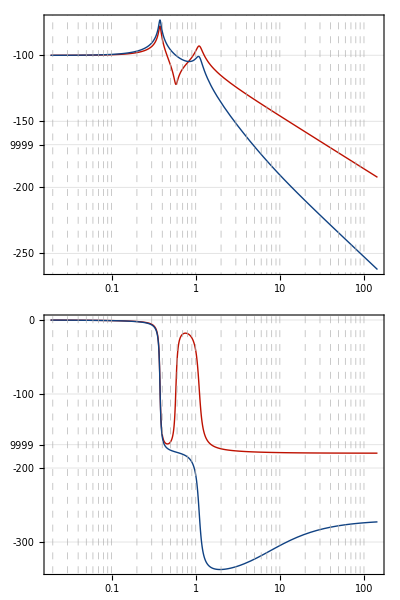

```mathematica
BodePlot[{XVF[[1,1,2]]/.{F1->1,F2->0},XVF[[1,1,2]]/.{F1->0,F2->1}},ImageSize->550,Frame->True,PlotStyle->{Directive[Thick,ColorData[20,1]],Directive[Thick,ColorData[20,9]]},Frame->False,AspectRatio->1/2.25,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.7],Dashed,PlotLegends->{"X1/F1","X1/F2"}]]
```

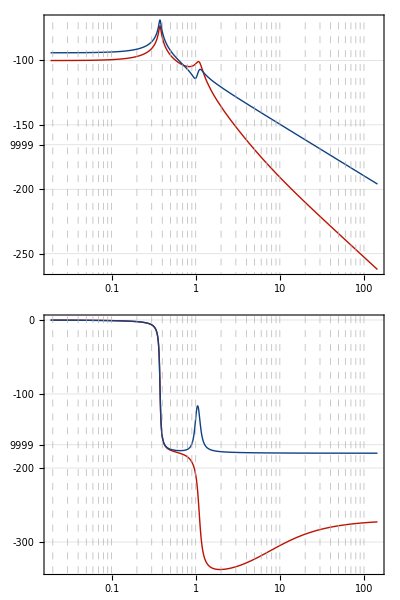

```mathematica
BodePlot[{XVF[[1,2,2]]/.{F1->1,F2->0},XVF[[1,2,2]]/.{F1->0,F2->1}},ImageSize->550,Frame->True,PlotStyle->{Directive[Thick,ColorData[20,1]],Directive[Thick,ColorData[20,9]]},Frame->False,AspectRatio->1/2.25,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.7],Dashed]]
```

## Manipulate the Bode Plot

```mathematica
XVF[[1,1,2]]
```

(F2 (1.6875×10^-6+2.33333×10^-7 s)+F1 (1.6875×10^-6+2.33333×10^-7 s+5.×10^-6 s^2))/(0.170859+0.04725 s+1.35327 s^2+0.186667 s^3+1. s^4)

```mathematica
BodePlot[{XVF[[1,1,2]]/.{F1->1,F2->0},XVF[[1,1,2]]/.{F1->0,F2->1}},ImageSize->550,Frame->True,PlotStyle->{Directive[Thick,ColorData[20,1]],Directive[Thick,ColorData[20,9]]},Frame->False,AspectRatio->1/2.25,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.7],Dashed]]
```

-Graphics-

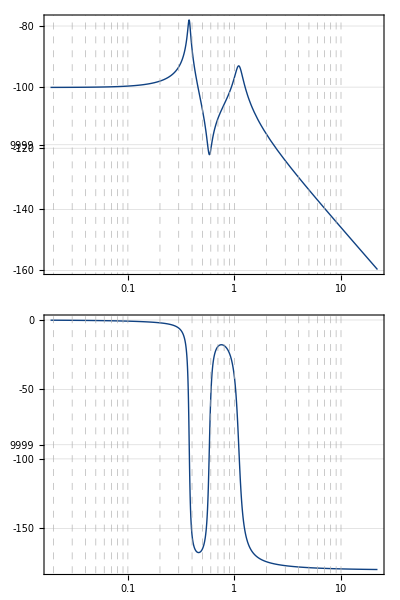

```mathematica
BodePlot[XVF[[1,1,2]]/.{F1->1,F2->0},ImageSize->550,Frame->True,PlotStyle->{Directive[Thick,ColorData[20,1]],Directive[Thick,ColorData[20,9]]},Frame->False,AspectRatio->1/2.25,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.7],Dashed]]
```

```mathematica
XVF[[1,1,2]]/.{s->ⅉ ω}
```

(F2 (1.6875×10^-6+(0.+2.33333×10^-7 ⅈ) ω)+F1 (1.6875×10^-6+(0.+2.33333×10^-7 ⅈ) ω-5.×10^-6 ω^2))/(0.170859+(0.+0.04725 ⅈ) ω-1.35327 ω^2-(0.+0.186667 ⅈ) ω^3+1. ω^4)

### Let’s investigate the influence of the two forces on the displacement of the first floor of the building.

```mathematica
Manipulate[Plot[
20*Log[(F2 (1.6875*10^-6+(0.+2.33333*10^-7 I) ω)+F1 (1.6875*10^-6+(0.+2.33333*10^-7 I) ω-5.*10^-6 ω^2))/(0.170859+(0.+0.04725 I) ω-1.35327 ω^2-(0.+0.186667 I) ω^3+1. ω^4)],
{ω,0,100}],
{F1,0,1},{F2,0,1}]
```